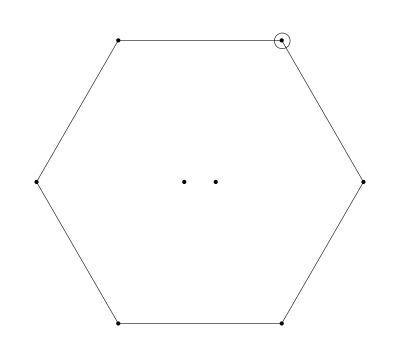

Y=1.5,  I_3=0.5

-2uu(ūs̄+s̄ū)-(ud+du)(s̄d̄+d̄s̄)-2(us+su)s̄s̄

```mathematica
(*-------------------------------*)
```

The current J:

(d_a^T C σ^αμ u_b) ((d̄)_b σ^αμ C((s̄)_a)^T-(s̄)_a σ^αμ C((d̄)_b)^T)+(u_a^T C σ^αμ d_b) ((d̄)_b σ^αμ C((s̄)_a)^T-(s̄)_a σ^αμ C((d̄)_b)^T)+(d_a^T C σ^αμ u_b) ((s̄)_b σ^αμ C((d̄)_a)^T-(d̄)_a σ^αμ C((s̄)_b)^T)+(u_a^T C σ^αμ d_b) ((s̄)_b σ^αμ C((d̄)_a)^T-(d̄)_a σ^αμ C((s̄)_b)^T)+2 ((s̄)_b σ^αμ C((s̄)_a)^T-(s̄)_a σ^αμ C((s̄)_b)^T) (s_a^T C σ^αμ u_b)+2 ((s̄)_b σ^αμ C((s̄)_a)^T-(s̄)_a σ^αμ C((s̄)_b)^T) (u_a^T C σ^αμ s_b)+2 (u_a^T C σ^αμ u_b) ((s̄)_b σ^αμ C((ū)_a)^T-(ū)_a σ^αμ C((s̄)_b)^T)+2 (u_a^T C σ^αμ u_b) ((ū)_b σ^αμ C((s̄)_a)^T-(s̄)_a σ^αμ C((ū)_b)^T)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
-12 (d̄(γ̄)^5 d+2 (s̄(γ̄)^5 s)) (s̄(γ̄)^5 u)-12 (d̄(γ̄)^5 u s̄(γ̄)^5 d)-2 (d̄ σ^μν d s̄ σ^μν u)-2 (d̄ σ^μν u s̄ σ^μν d)-12 (d̄ 1d+2 (s̄ 1s)) (s̄ 1u)-12 (d̄ 1u s̄ 1d)-24 (s̄(γ̄)^5 u ū(γ̄)^5 u)-4 (s̄ σ^μν s s̄ σ^μν u)-4 (s̄ σ^μν u ū σ^μν u)-24 (s̄ 1u ū 1u)
```

Π(q^2)=
-(log(-q^2/μ^2) q^8)/(32 π^6)-(5 ⟨ GG ⟩ log(-q^2/μ^2) q^4)/(12 π^5)-(2 ⟨ d̄ d⟩ log(-q^2/μ^2) m_d q^4)/π^4-(9 ⟨ s̄ s⟩ log(-q^2/μ^2) m_s q^4)/π^4-(9 ⟨ ū u⟩ log(-q^2/μ^2) m_u q^4)/π^4-(24 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/π^2-(96 ⟨ s̄ s⟩^2 log(-q^2/μ^2) q^2)/π^2-(96 ⟨ ū u⟩^2 log(-q^2/μ^2) q^2)/π^2+(5 ⟨G^3⟩ log(-q^2/μ^2) q^2)/(4 π^6)-(96 ⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/π^2-(96 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/π^2-(192 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/π^2+(8 ⟨ d̄ d⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/π^2+(16 ⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/π^2+(16 ⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/π^2+(16 ⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/π^2+(32 ⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/π^2+(32 ⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/π^2+(16 ⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/π^2+(32 ⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/π^2+(32 ⟨ ū u⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/π^2-(8 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(π q^2)-(32 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(π q^2)-(32 ⟨ GG ⟩ ⟨ ū u⟩^2)/(π q^2)-⟨ d̄ Gd⟩^2/(6 π^2 q^2)-(2 ⟨ s̄ Gs⟩^2)/(3 π^2 q^2)-(2 ⟨ ū Gu⟩^2)/(3 π^2 q^2)-(32 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(π q^2)-(32 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(π q^2)-(64 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(π q^2)-(2 ⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(3 π^2 q^2)-(2 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(3 π^2 q^2)-(4 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(3 π^2 q^2)-(128 ⟨ d̄ d⟩ ⟨ ū u⟩^2 (2 m_s+m_u))/q^2-(128 ⟨ d̄ d⟩ ⟨ s̄ s⟩^2 (m_s+2 m_u))/q^2-(16 ⟨ d̄ d⟩^2 ⟨ s̄ s⟩ (6 m_s+4 m_u))/(3 q^2)-(64 ⟨ s̄ s⟩ ⟨ ū u⟩^2 (10 m_s+4 m_u))/q^2-(16 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (4 m_s+6 m_u))/(3 q^2)-(64 ⟨ ū u⟩^3 (8 m_s+6 m_u))/(3 q^2)-(64 ⟨ s̄ s⟩^3 (6 m_s+8 m_u))/(3 q^2)-(64 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (4 m_s+10 m_u))/q^2-(64 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ (18 (m_s+m_u)-4 m_d))/(3 q^2)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=η_8=η_10=1

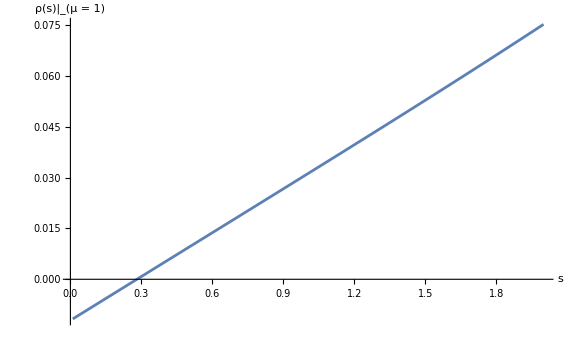
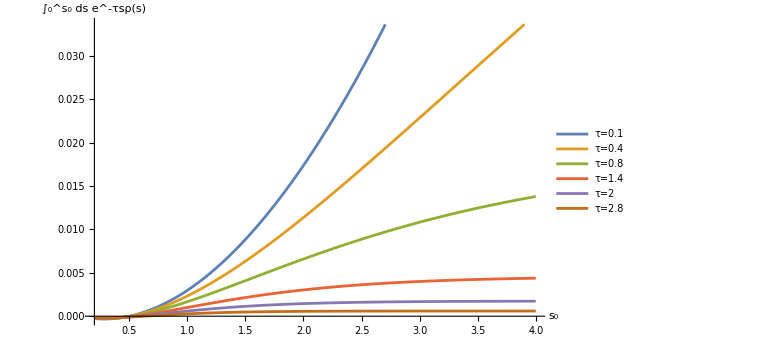

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=η_8=η_10=1

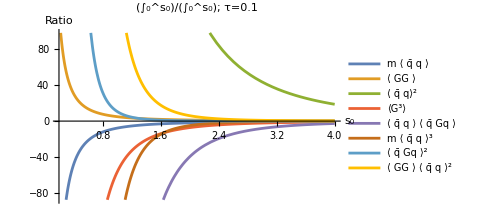
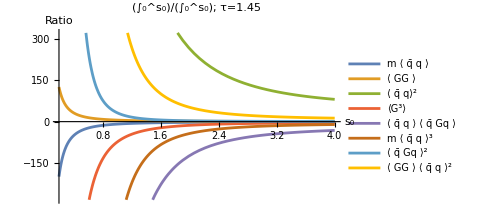
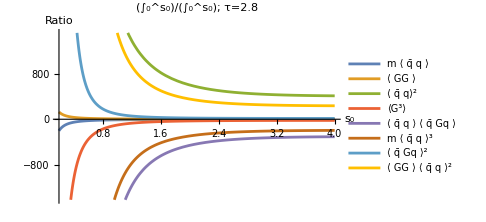

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=η_8=η_10=1

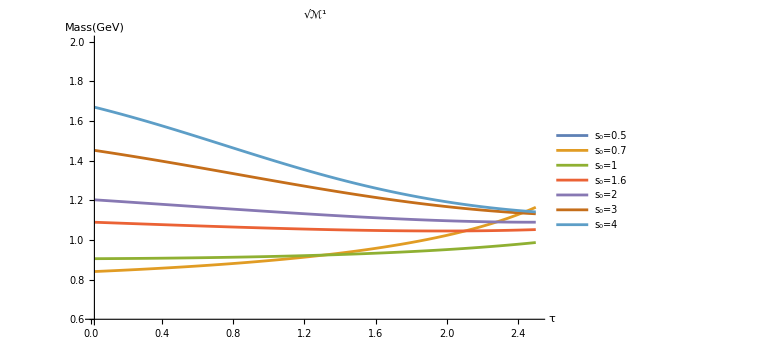
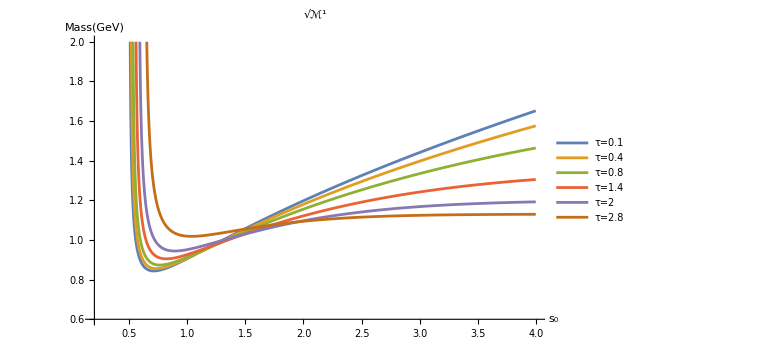

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=η_8=η_10=1

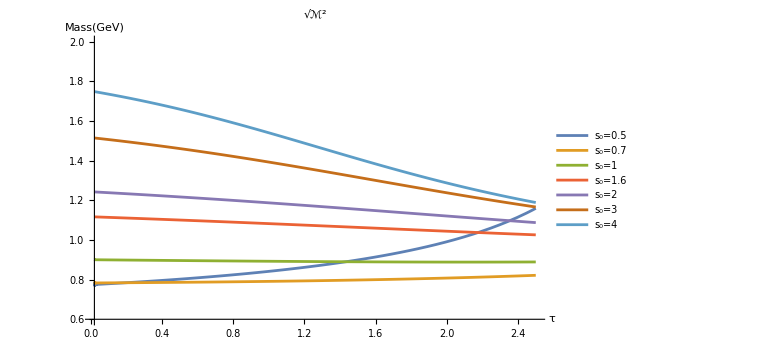
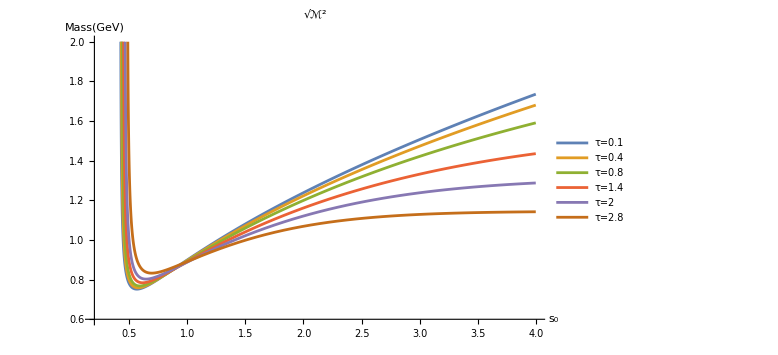

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=3, η_8=5, η_10=5

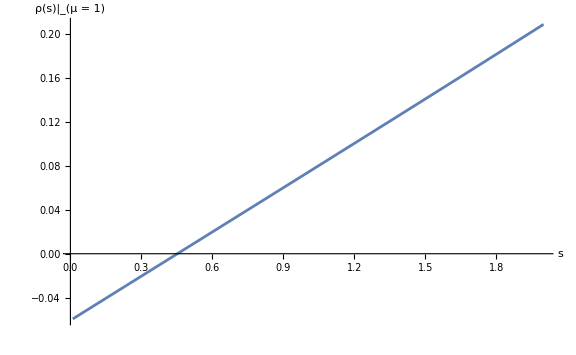
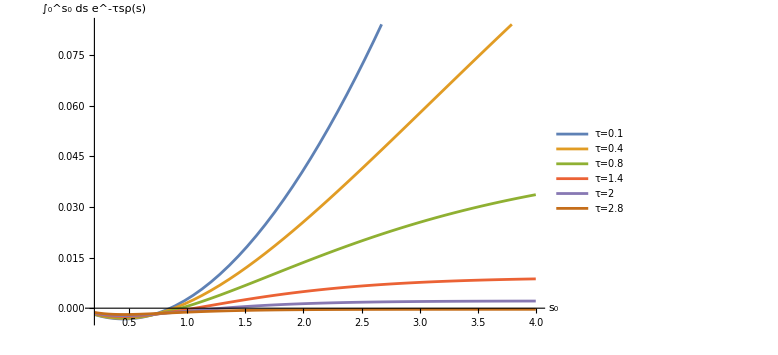

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=3, η_8=5, η_10=5

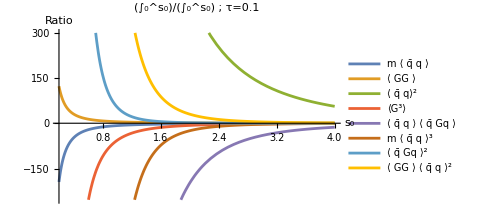
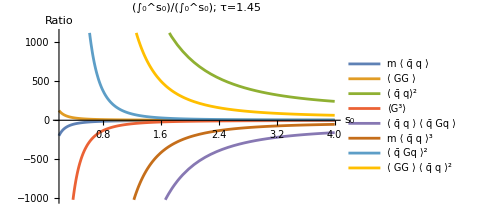
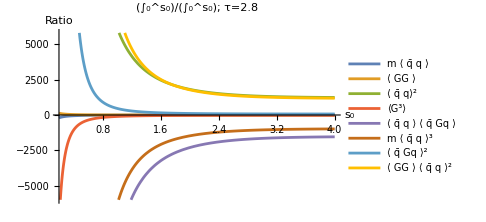

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=3, η_8=5, η_10=5

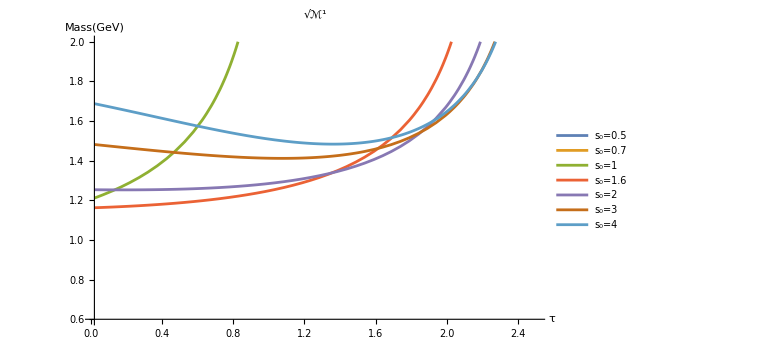
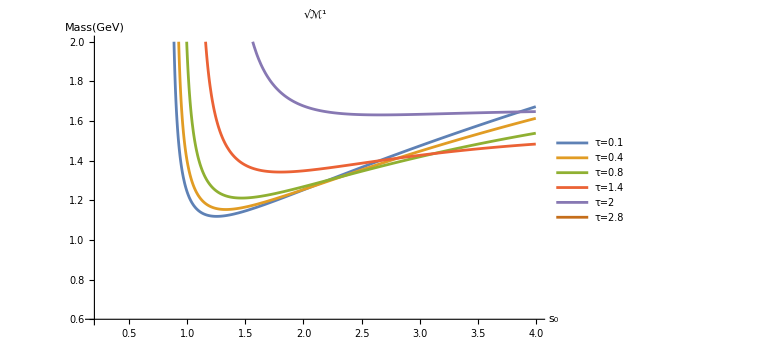

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=3, η_8=5, η_10=5